## Periods

```mathematica
Quit
```

```mathematica
(*PRIMER PERIODO*)
Num = 200; 
sample =3;
(* Operador de Piccard-Fuchs, z es la estructura compleja, F es el período sobre el que actúa*)
PF[z_,F_]:= (z D[#,z])&[(z D[#,z])&[(z D[#,z])&[z D[#,z]& [F]]]]-z 2^4 (2z D[#,z]+1 #)&[(2z D[#,z]+1#)&[(2 z D[#,z]+1 #)&[(2z D[#,z]+1#)&[F]]]]
c2D = 64; k = 16; χ = -128;
(* Ansatz polinomial*)
AnsaM[z_, x_, N_] := z^x Sum[f[n] z^n, {n, 0, N}]
(* Aplicar el operador en el Ansatz*)
tri = PF[z, AnsaM[z, x, Num]] // Expand ;
(*Print["EVALUACIÓN DEL ANSATZ EN EL OPERADOR"]*)
(*L(wM1)= *)Take[tri,sample];
var=Table[f[i],{i,1,Num}];
Clear[c];
(* Tomamos los coeficientes de las potencias de z*)
(*Print["Ecuaciones de recurrencia "];*)
Do[Coefficient[tri/.{x->0},z,k]==0,{k,1,sample}]
f[0]=1;
(* Resolvemos para el Ansatz dado*)
solM[0]=Solve[Table[Coefficient[tri/.{x->0},z,k]==0,{k,1,Num}],var][[1]];
Clear[f];
solM[0]=Join[{f[0]->1},solM[0]];
(*Soluciones *)Take[solM[0],sample];
SMum[z_,0,N_]:=AnsaM[z,0,N]/.solM[0];
Take[SMum[z,0,Num],sample];
wM0=SMum[z,0,Num];
Print["1st Period Π_1(...)= ",Take[wM0,sample]]
(*Print["1st Period Π_1(...)= ",Take[SMum[z,0,Num]//Expand,5]];*)
(*SEGUNDO PERIODO*)
(*Ansatz  wM1, con monodromía*)
AnsaBM[z_,xb_,Num_]:=z^xb Sum[b[k]z^k,{k,0,Num}];
(*Nuevo ansatz ","w0M Log[z] +w1M, w1M=z^xb ( b[0]+b[1]z+b[2]z^2... )"];*)
Clear[TotM];
TotM=Expand[PF[z,Log[z]*wM0]]+PF[z,AnsaBM[z,xb,Num]]//Expand;
(*L (w0M Log[z]+w1M)= *)Take[TotM,sample];
(*El coeficiente z^xb en L (w0M Log[z]+w1M) es*)Take[Coefficient[TotM,z,xb],2sample];
(*El coeficiente z^0 en L (w0M Log[z]+w1M) es *) Coefficient[TotM,z,0];
var2=Table[b[k],{k,0,Num}];
(*Ecuaciones :*)Table[Coefficient[TotM/.{xb->1},z,k]==0,{k,1,Num}];
solbM=Solve[Table[Coefficient[TotM/.{xb->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Soluciones *)Take[solbM,sample];
Do[{z^k,Coefficient[TotM[x]/.xb->1/.solbM,z,k]},{k,Num-1,Num+3}];
Clear[w0,w1];
w0[z_]:=AnsaM[z,0,Num]/.solM[0];
w1[z_]:=AnsaBM[z,1,Num]/.solbM;
SMum[z_,1,Num]:=w0[z]Log[z]+w1[z];
Take[SMum[z,1,Num]//Expand,sample];
wM1= wM0 Log[z]+w1[z]//Expand;
(*Print["2nd Period Π_2(...)= ",wM1];*)
Print["2st Period Π_2(...)= ",Take[wM1,sample]];
(*TERCER PERIODO*)
(*Nuevo ansatz*)
(*Nuevo ansatz  wM0 Log[z]^2+2w1M Log[z]+w2M "];*)
Take[Log[z]^2*w0[z]+2Log[z]w1[z]//Expand,sample];
AnsaC[z_,xc_,Num_]:=z^xc Sum[d[k]z^k,{k,0,Num}]
(*w2M= *)Take[AnsaC[z,xc,Num]//Expand,sample]//Factor;
Clear[Tot2];
Tot2=PF[z,Log[z]^2*w0[z]+2Log[z]w1[z]]+PF[z,AnsaC[z,xc,Num]];
(*L(wM0 Log[z]^2+2 Log[z] wM1+wM2)= *)Take[Tot2//Expand,sample]//Expand;
(*L(wM0 Log[z]^2+2 Log[z] wM1)=*)Take[PF[z,Log[z]^2*w0[z]+2Log[z]w1[z]]//Expand,sample];
(*Coeficiente en L(wM0 Log[z]^2+2 Log[z] wM1+wM2) de z^xc *)Coefficient[Tot2,z,xc]/.{z->0};
(*Eval. xc->1  Coef. z^1 *)Coefficient[Tot2/.{xc->1},z,1];
(*Eval. xc->1  Coef. z^2 *)Coefficient[Tot2/.{xc->1},z,2];
var2=Table[d[k],{k,0,Num}];
solc=Solve[Table[Coefficient[Tot2/.{xc->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]] ;
w2[z_]:=AnsaC[z,xc,Num]/.xc->1/.solc ;
w2[z]//Expand ;
(*w2 = *)Take[w2[z]//Expand,sample];
Do[{z^k,Coefficient[Tot2/.xc->1/.solc,z,k]},{k,Num-3,Num+3}];
(*Ecuaciones *)Table[Coefficient[Tot2/.{xc->1},z,i]==0,{i,0,sample}];
(*Soluciones*)Take[solc,sample];
w2[z_]:=AnsaC[z,1,Num]/.solc;
SMum[z_,2,Num]:=Log[z]^2*w0[z]+2Log[z]w1[z]+w2[z] ;
wM2= 1/2 Log[z]^2*wM0+  Log[z]wM1+  w2[z]//Expand ;
Print["3dt Period Π_3(...)= ", Take[wM2,sample]] 
(*CUARTO PERIODO*)
(*SOLUCION    w0 Log[z]^3+3w1 Log[z]^2+3w2 Log[z]+w3*)
(*NUEVO ANSATZ wM0 Log[z]^3+3 wM1 Log[z]^2+3wM2 Log[z]+wM3 : *)
Clear[AnsaD,var];
AnsaD[z_,xd_,Num_]:=z^xd Sum[e[k]z^k,{k,0,Num}];
(*Print[AnsaD[z,xd,sample]*)
Clear[Tot3];
Tot3=PF[z,Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]]+PF[z,AnsaD[z,xd,Num]]//Expand;
var2=Table[e[k],{k,0,Num}];
(*L (Ansatz)"*)
(*Coeficiente z^xd(...) en L (Ansatz) *)Take[Coefficient[Tot3,z,xd],sample];
(*Coeficiente z(...) en L (Ansatz)*)Coefficient[Tot3/.{xd->1},z,1];
(*Coeficiente z^2(...) en L (Ansatz) *)Coefficient[Tot3/.{xd->1},z,2];
(*remanente*)
sold=Solve[Table[Coefficient[Tot3/.{xd->1},z,k]==0/.{Log[z]:>0},{k,1,Num+1}],var2][[1]];
(*Remanente Coeficientes en L (Ansatz) *)Table[Coefficient[Tot3/.{xd->1}/.sold//N,z,i],{i,Num-5,Num+5}];
(*Remanente en L (Ansatz) *)Tot3/.xd->1/.sold//N;
(*Soluciones ansatz  wM3[z]=z^xd (d[0]+z d[1]+z^2 d[2]+...*)Take[sold,sample];
(*Terminos remanentes en L Ansatz "*)
Do[{z^k,Coefficient[Tot3/.xd->1/.sold,z,k]//N},{k,Num-2,Num+3}];
Clear[w3];
w3[z_]:=AnsaD[z,1,Num]/.sold ;
SMum[z_,3,Num]:=5/6(Log[z]^3*w0[z]+3Log[z]^2w1[z]+3Log[z]w2[z]+w3[z])//Expand;
(*wM3= *)Take[5/6w3[z]//Expand,sample];
(*Print["4ht Period Π_4(...)=  ",Take[SMum[z,3,Num],sample],"... + ",Log[z]Take[Coefficient[SMum[z,3,Num],Log[z]],sample],"... + ",Log[z]^2Take[Coefficient[SMum[z,3,Num],Log[z]^2],sample],"... + "Log[z]^3Take[Coefficient[SMum[z,3,Num],Log[z]^3],sample],"..."];*)
wM3= 1/6 Log[z]^3 wM0 + 1/2 Log[z]^2 wM1 +  Log[z]wM2 +  w3[z] // Expand;
Print["4ht Period Π_4(...)=  ",Take[wM3,sample]]
```

1st Period Π_1(...)= 1+16 z+1296 z^2

2st Period Π_2(...)= 64 z+6048 z^2+(2368000 z^3)/3

3dt Period Π_3(...)= 64 z+11664 z^2+(16364800 z^3)/9

4ht Period Π_4(...)=  -384 z-25776 z^2-(20668160 z^3)/9

```mathematica
NCF=1;
FluxesM={{-4,-4,-2,3,-1,-6,8,6}};
SolTableDeSitAKM=Table[{0,0,0,0},NCF];
DerivScalarPot=Table[{0,0,0,0,0},NCF];
$MinPrecision=50;
(*SetPrecision[$MinMachineNumber,$MachinePrecision]*)
(*exact=20;*)
(* todo lo que importas y exportas es de la carpeta dodne est'a el programa*)
Clear[K,PiC0,PiC,W,Wc,X,x,Σ,Πc,Π,sel];
(*flujos*)
(*serie para los periodos*)
Num=200;
sel=100;
l=1;
rvalues=Table[0,10];
tau2values=Table[0,10];
Do[
 PiC={wM0,wM1,wM2,wM3};
(*Se forma un arreglo conteniendo las componentes de periodos*) 
PiC2={Take[PiC[[1]],sel],Take[PiC[[2]]//Expand,sel-1]+Take[Coefficient[PiC[[2]]//Expand,Log[z]],sel]Log[z],Take[PiC[[3]]//Expand,sel-1]+Take[Coefficient[PiC[[3]]//Expand,Log[z]],sel-1]Log[z]+Take[Coefficient[PiC[[3]]//Expand,Log[z]^2],sel]Log[z]^2,
Take[PiC[[4]]//Expand,sel-1]+Take[Coefficient[PiC[[4]]//Expand,Log[z]],sel-1]Log[z]+Take[Coefficient[PiC[[4]]//Expand,Log[z]^2],sel-1]Log[z]^2+Take[Coefficient[PiC[[4]]//Expand,Log[z]^3],sel]Log[z]^3};
c2D = 64;
k = 16;
χ = -128;
sigma = 1;
reimann = N[Zeta[3]];

trans =((2π ⅈ)^3 ){{(reimann*χ)/((2π ⅈ)^3), c2D/(24 * 2 π ⅈ), 0, k/(2π ⅈ)^3}, {c2D/(24),1/(2π ⅈ), -k/(2π ⅈ)^2, 0 }, {1, 0, 0, 0}, {0,1/(2 π ⅈ) , 0, 0} };
Π[z_]:=Chop[SetPrecision[(trans.(PiC2)),50],Power[10,-50]];
If[sel≠1,
Πc[zc_]:=Expand[Table[Plus@@(Conjugate[List@@(Π[z][[k]]//Expand)]/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}),{k,1,4}]],
Πc[zc_]:=(Conjugate[Π[z]]//Expand)/.{Conjugate[z]->zc, Conjugate[Log[z]]-> Log[zc],
Conjugate[z Log[z]]-> zc Log[zc]}];

(*Matriz Simplectica*)
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};


Do[
(*Definición de flujos*)
n1=1;n2=1;
Clear[H,F,H1,H2,H3,H4,F1,F2,F3,F4];
H1=H[1]=FluxesM[[m]][[1]]*n1;(*1*)
H2=H[2]=FluxesM[[m]][[2]]*n1;
H3=H[3]=FluxesM[[m]][[3]]*n1;
H4=H[4]=FluxesM[[m]][[4]]*n1;
F1=F[1]=FluxesM[[m]][[5]]*n2;
F2=F[2]=FluxesM[[m]][[6]]*n2;
F3=F[3]=FluxesM[[m]][[7]]*n2;
F4=F[4]=FluxesM[[m]][[8]]*n2;

(* 3-form flux-Forma G3*)
X[t_]:={F1,F2,F3,F4}-t{H1,H2,H3,H4};

(* Potencial de Kaehler*)
K[t_,tc_,z_,zc_]:=-Log[-I(t-tc)]-Log[-I Πc[zc].Σ.Π[z]];
(* superpotencial*)
W[t_,z_]:=X[t].Σ.Π[z];
(*superpotencial conjugado*)
Wc[tc_,zc_]:=X[tc].Σ.Πc[zc];

(*  G_{z zc}*)
g11=((D[ Πc[zc],zc].Σ.Π[z] )(Πc[zc].Σ.D[Π[z],z]))/( Πc[zc].Σ.Π[z])^2-(D[Πc[zc],zc].Σ.D[Π[z],z])/( Πc[zc].Σ.Π[z]);

(*redfinicion a cos y senos*)
rep=Flatten[Table[{Exp[I p n ]-> Cos[n p]+I Sin[n p],Exp[-I p n]-> Cos[n p]-I Sin[n p]},{n,1,100}]];

(* derivadas covariantes*)
Clear[Dcv,Dcv2,G,PM,t,tc];
Dcv[x_,1]:=(D[x,z]+x D[K[t,tc,z,zc],z]);
Dcv[x_,2]:=(D[x,t]+x D[K[t,tc,z,zc],t]);(*chequear*)

(* derivadas covariantes conjugadas*)
Dcv2[x_,1]:=(D[x,zc]+x D[K[t,tc,z,zc],zc]);
Dcv2[x_,2]:=(D[x,tc]+x D[K[t,tc,z,zc],tc]);

 (* Matriz Pi tilde en el paper*)
PMt=-Table[Π[z][[i]]D[Π[z][[j]],z]-Π[z][[j]]D[Π[z][[i]],z],{i,1,4},{j,1,4}];
(* derivadas covariantes del superpotencial*)
DzW=(Πc[zc].Σ.Transpose[PMt]).(X[t].Σ)/(Πc[zc].Σ.Π[z]);
DtW=(tc {H1,H2,H3,H4}-{F1,F2,F3,F4} ).(Σ.Π[z])/(t-tc);

(* metrica de Kaehler*)
G[1,1]=D[K[t,tc,z,zc],z,zc];
G[2,2]=D[K[t,tc,z,zc],t,tc];
G[2,1]=D[K[t,tc,z,zc],t,zc];
G[1,2]=D[K[t,tc,z,zc],z,tc];

(* Matriz Pi tilde en el paper*)
PM[z_,i_,j_]:=-(Π[z][[i]]D[Π[z][[j]],z]-Π[z][[j]]D[Π[z][[i]],z]);

(* potencial de Kaehler en coordenadas polares*)
Kr[t_,tc_,r_,p_]:=(K[t,tc,z,zc]/.{Log[z]->Log[r]+I p,Log[zc]->Log[r]-I p})/.{z->r (Cos[p]+I Sin[p]),zc->r (Cos[p]-I Sin[p])};
(* potencial escalar en coordendas z zc y t tc*)
Clear[Vcomp];
Vcomp=SetPrecision[Exp[K[t,tc,z,zc]]((1/G[1,1])Dcv2[Wc[tc,zc],1]Dcv[W[t,z],1]+(1/G[2,2])Dcv2[Wc[tc,zc],2]Dcv[W[t,z],2]),50];

(* cambio a polares de g11*)
g11R=(g11/.{t->I ,tc->-I ,Log[z]->Log[r]+I phi,Log[zc]->Log[r]-I phi})/.{z->r Exp[I phi],zc->r Exp[-I phi]};
(*ecuaciones para vacio con conifold monodromies*)

(* monodromias alrededor del conifold*)

Tc=IdentityMatrix[4]+{{0,0,0,0},{0,0,0,0},{-1(*ver esto*),0,0,0},{0,0,0,0}};

(*Tc2=IdentityMatrix[4]+{{0,0,0,0},{0,0,0,0},{-1(*igual mondromia*),0,0,0},{0,0,0,0}};*)
Clear[T];
T[n_]:=If[n≥ 0,MatrixPower[Tc,n],MatrixPower[Inverse[Tc],-n]];
(*Print[Tc//MatrixForm];*)

(* ecuacion para vacios de Minkowski,  anadiendo monodromias*)
busco3[n_]:=SetPrecision[Sum[F[i]Σ[[i,j]](T[n].Πc[zc])[[j]],{i,1,4},{j,1,4}]Sum[H[i]Σ[[i,j]](T[n].Πc[zc])[[k]]Σ[[k,l]](T[n].PMt.Transpose[T[n]])[[j,l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]-
Sum[H[i]Σ[[i,j]](T[n].Πc[zc])[[j]],{i,1,4},{j,1,4}]Sum[F[i]Σ[[i,j]](T[n].Πc[zc])[[k]]Σ[[k,l]](T[n].PMt.Transpose[T[n]])[[j,l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}],50];

prueba3f[n_]:= SetPrecision[Sum[H[i]Σ[[i,j]](T[n].Πc[zc])[[j]],{i,1,4},{j,1,4}] Sum[F[i]Σ[[i,j]]T[0][[j,k]]PMt[[k,l]](Transpose[T[0]].Σ.T[0])[[l,ii]]Πc[zc][[ii]],{i,1,4},{j,1,4},{k,1,4},{l,1,4},{ii,1,4}]-Sum[F[i]Σ[[i,j]](T[n].Πc[zc])[[j]],{i,1,4},{j,1,4}] Sum[H[i]Σ[[i,j]]T[0][[j,k]]PMt[[k,l]](Transpose[T[0]].Σ.T[0])[[l,ii]]Πc[zc][[ii]],{i,1,4},{j,1,4},{k,1,4},{l,1,4},{ii,1,4}],50];

(* tau_{tau}*)
Clear[TauT];
TauT=Sum[F[i]Σ[[i,j]]Πc[zc][[j]],{i,1,4},{j,1,4}]/
Sum[H[i]Σ[[i,j]]Πc[zc][[j]],{i,1,4},{j,1,4}];

TauT2=(TauT/.{Log[z]->Log[r]+I p}/.{Log[zc]->Log[r]-I p}/.{z->r Exp[I p],zc->r Exp[-I p]}/.rep);

(* ecuacion de vacios de mInkowski sin monodromia*)
(*Clear[busco4];mon=0;
busco30=prueba3f[mon];
busco4=ReplaceAll[ReplaceAll[busco30,{Log[zc]->-I p+Log[r],Log[z]->I p+Log[r]}],{z->r (Cos[p]+I Sin[p]),zc->r (Cos[ p]-I Sin[p])}]/.rep;b4IM=Im[busco4]; b4Re=Re[busco4];*)

(* ecuaciones vacios de Minkowski*)
(*solus0[m]=Table[sol=FindRoot[{b4IM,b4Re},{{r,0.000005},{p,2 Pi k}},WorkingPrecision->50,MaxIterations->1000],{k,-10,10}];*)
(*solus0[m]=sol=FindRoot[{b4IM,b4Re},{{r,0.000005},{p,20 Pi }},WorkingPrecision->50,MaxIterations->1000];
G11=(G[1,1]/.{Log[z]->Log[r]+I p}/.{Log[zc]->Log[r]-I p}/.{z->r Exp[I p],zc->r Exp[-I p]}/.rep);
tau2M=Im[TauT2/.sol];*)


(* imprime cero de la ecuacion*)
(*Print["Soluciones de vacio Minkowski ",{busco4/.sol,sol}];*)
(* metrica de Kaehler en la solucion *)
(*Print["Metrica de Kaehler Gzzc ",G11/.sol];*)

(*******POSIBLES SOLUCIONES DE DE SITTER********)
Clear[DzV,DzcV,DtV,DtcV,tau1,tau2,dVsol,V];
DzV=ReplaceAll[ReplaceAll[D[Vcomp,z],{Log[zc]->-I p+Log[r],Log[z]->I p+Log[r]}],{z->r (Cos[p]+I Sin[p]),zc->r (Cos[ p]-I Sin[p]),t->tau1+I tau2,tc->tau1-I tau2}]/.rep;
DzcV=ReplaceAll[ReplaceAll[D[Vcomp,zc],{Log[zc]->-I p+Log[r],Log[z]->I p+Log[r]}],{z->r (Cos[p]+I Sin[p]),zc->r (Cos[ p]-I Sin[p]),t->tau1+I tau2,tc->tau1-I tau2}]/.rep;
DtV=ReplaceAll[ReplaceAll[D[Vcomp,t],{Log[zc]->-I p+Log[r],Log[z]->I p+Log[r]}],{z->r (Cos[p]+I Sin[p]),zc->r (Cos[ p]-I Sin[p]),t->tau1+I tau2,tc->tau1-I tau2}]/.rep;
DtcV=ReplaceAll[ReplaceAll[D[Vcomp,tc],{Log[zc]->-I p+Log[r],Log[z]->I p+Log[r]}],{z->r (Cos[p]+I Sin[p]),zc->r (Cos[ p]-I Sin[p]),t->tau1+I tau2,tc->tau1-I tau2}]/.rep;

(*dVsol=FindRoot[{DzV==0,DzcV==0,DtV==0,DtcV==0},{{r,0.0005},{p,2*Pi},{tau1,.0005},{tau2,.01}},WorkingPrecision->50,DampingFactor->2,MaxIterations->10000]*)

(*dVsol=FindRoot[{DzV==0,DzcV==0,DtV==0,DtcV==0},{{r,0.0005,.9},{p,2*Pi},{tau1,.0005},{tau2,.01}},WorkingPrecision->50,DampingFactor->1,MaxIterations->10000,StepMonitor:>c++]*)
cc=0;
dVsol=FindRoot[{DzV==0,DzcV==0,DtV==0,DtcV==0},{{r,0.0001},{p,Pi/4},{tau1,.0005},{tau2,.01}},WorkingPrecision->50,MaxIterations->10000,StepMonitor:>cc++];
Print["Steps"->cc]
(**) 
(*{r,0.0001},{p,Pi/4},{tau1,.0005},{tau2,.01} IMPORTANTE*)
(*{r,.005},{p,Pi },{tau1,.0005},{tau2,.0005}*)
(*{r,.00005},{p,2 Pi *1},{tau1,.0000005},{tau2,.01}*)
(*{{r,5/(10^5)},{p,2 Pi *1},{tau1,5/(10^7)},{tau2,1/(10^2)}*)
(* FindRoot[{DzV,DzcV,DtV,DtcV},{{r,.00005},{p,2 Pi *1},{tau1,.0000005},{tau2,.01}},WorkingPrecision->50,MaxIterations->10000] *)
(*Print["Soluciones DeSitter",dVsol];*)
Clear[V,VM];
V=ReplaceAll[ReplaceAll[Vcomp,{Log[zc]->-I p+Log[r],Log[z]->I p+Log[r]}],{z->r (Cos[p]+I Sin[p]),zc->r (Cos[ p]-I Sin[p]),t->tau1+I tau2,tc->tau1-I tau2}]/.rep/.dVsol;
(*VM=ReplaceAll[ReplaceAll[Vcomp,{Log[zc]->-I p+Log[r],Log[z]->I p+Log[r]}],{z->r (Cos[p]+I Sin[p]),zc->r (Cos[ p]-I Sin[p]),t->TauT2,tc->Conjugate[TauT2]}]/.rep/.sol;*)

(*Print["Potencial evaluado en la solucion V= ",V];*)
(*Clear[Vm,Gzzc0,Vme,Mmass,Mmasseig,eigenmin,VmeM,MmassM,MmasseigM,eigenminM];
Gzzc0=ReplaceAll[ReplaceAll[G[1,1],{Log[zc]->-I p+Log[r],Log[z]->I p+Log[r]}],{z->r (Cos[p]+I Sin[p]),zc->r (Cos[ p]-I Sin[p]),t->tau1+I tau2,tc->tau1-I tau2}]/.rep/.dVsol;
Vm=ReplaceAll[ReplaceAll[Vcomp,{Log[zc]->-I p+Log[r],Log[z]->I p+Log[r]}],{z->r (Cos[p]+I Sin[p]),zc->r (Cos[ p]-I Sin[p]),t->tau1+I tau2,tc->tau1-I tau2}]/.rep;
PPV=D[Vm,{{r,p,tau1,tau2}},{{r,p,tau1,tau2}}];
Vme=PPV/.dVsol;
(*VmeM=ReplaceAll[PPV/.sol,{tau1->Re[TauT2/.sol],tau2->Im[TauT2/.sol]}]/.rep;*)

c[1]=1/Sqrt[Gzzc0];c[2]=1/(Sqrt[Gzzc0]*r)/.dVsol; c[3]=c[4]=(2*tau2)/.dVsol;

Mmass=Table[c[i]c[j]Vme[[i,j]],{i,1,4},{j,1,4}];
(*Adding the Kahler modulus rho*)
(*Mmassρ=*)
Clear[M3,Mmassρ,Imρ];
M3=Chop[Mmass,Power[10,-50]];
Mmassρ=ConstantArray[0,{5,5}] ;
Imρ=(1/2)*(10^4)^(2/3);
For[i=1,i<5,i++,
For[j=1,j<5,j++, Mmassρ[[i,j]] =M3[[i,j]]*(1/(2*Imρ)^3)  ]
];
Mmassρ[[5,5]]=(3/(2*(Imρ)^5))*Chop[V,Power[10,-20]];
Mmasseig=Eigenvalues[Mmassρ];
eigenmin=Min[Chop[Mmasseig,Power[10,-20]]];*)
(*Vscalar=V*Exp[-2Log[(2*Imρ)^(3/2)]];*)

(*cM[1]=1/Sqrt[G11/.sol];cM[2]=1/(Sqrt[G11/.sol]*r)/.sol; cM[3]=cM[4]=(2*Im[TauT2/.sol])/.dVsol;
MmassM=Table[cM[i]cM[j]VmeM[[i,j]],{i,1,4},{j,1,4}];
MmasseigM=Eigenvalues[MmassM]
(*Print[Mmasseig];*)
eigenminM=Min[Chop[MmasseigM,Power[10,-5]]]*)

(*Almacenado datos en arreglo: m,V,r,p,tau2,mineigen*)
SolTableDeSitAKM[[m]]={m,Chop[V,Power[10,-50]],r/.dVsol,p/.dVsol,tau2/.dVsol};
(*SolTableMink[[m]]={m,VM,r/.sol,p/.sol,tau2M};*) (*Almacenado datos en arreglo: Gzzc,r,p*)

DerivScalarPot[[m]]={m,DzV/.dVsol,DzcV/.dVsol,DtV/.dVsol,DtcV/.dVsol};
NotebookDelete[Casescount];
Casescount=PrintTemporary["Case: ",m,"/",NCF];
,{m,NCF}];
rvalues[[l]]=r/.dVsol;
tau2values[[l]]=tau2/.dVsol;
PrintTemporary[sel];
l=l+1;
,{sel,{100}}];
Print["DONE! :)"];
```

Steps→33

DONE! :)

```mathematica
dVsol
```

{r→0.0038982627244953723071093837692684805980015732472507+2.8045788262206315235804088458368274172549415904994×10^-63 ⅈ,p→0.24974621594968777809590773063431465018387720021878+5.2341544766037626386240830132932248822660116705886×10^-61 ⅈ,tau1→-1.2214265545494748157014894784071121961939014630987-9.4229102413094415040976359127413729183097999191796×10^-61 ⅈ,tau2→2.6236117391903211701953159959094561600202203343949-4.9490569716249164080183407122400906505296185365859×10^-60 ⅈ}

```mathematica
V
```

181.0023193875071838045751714248308575222525926436+2.9946631485892442591772094412745338390935150895871×10^-59 ⅈ

```mathematica
(* Valor del vacío*)
SolTableDeSitAKM
dVsol;
Vr=(ReplaceAll[ReplaceAll[Vcomp,{Log[zc]->-I p+Log[r],Log[z]->I p+Log[r]}],{z->r (Cos[p]+I Sin[p]),zc->r (Cos[ p]-I Sin[p]),t->tau1+I tau2,tc->tau1-I tau2}]/.rep)/.Drop[dVsol,1];
Vp=(ReplaceAll[ReplaceAll[Vcomp,{Log[zc]->-I p+Log[r],Log[z]->I p+Log[r]}],{z->r (Cos[p]+I Sin[p]),zc->r (Cos[ p]-I Sin[p]),t->tau1+I tau2,tc->tau1-I tau2}]/.rep)/.Drop[dVsol,{2}];
Vt1=(ReplaceAll[ReplaceAll[Vcomp,{Log[zc]->-I p+Log[r],Log[z]->I p+Log[r]}],{z->r (Cos[p]+I Sin[p]),zc->r (Cos[ p]-I Sin[p]),t->tau1+I tau2,tc->tau1-I tau2}]/.rep)/.Drop[dVsol,{3}];
Vt2=(ReplaceAll[ReplaceAll[Vcomp,{Log[zc]->-I p+Log[r],Log[z]->I p+Log[r]}],{z->r (Cos[p]+I Sin[p]),zc->r (Cos[ p]-I Sin[p]),t->tau1+I tau2,tc->tau1-I tau2}]/.rep)/.Drop[dVsol,{4}];
dVsol;
Drop[dVsol,{4}];
r0=Chop[r/.dVsol];
p0=Chop[p/.dVsol];
t10=Chop[tau1/.dVsol];
t20=Chop[tau2/.dVsol];
r0;
p0;
```

{{1,181.0023193875071838045751714248308575222525926436,0.0038982627244953723071093837692684805980015732472507+2.8045788262206315235804088458368274172549415904994×10^-63 ⅈ,0.24974621594968777809590773063431465018387720021878+5.2341544766037626386240830132932248822660116705886×10^-61 ⅈ,2.6236117391903211701953159959094561600202203343949-4.9490569716249164080183407122400906505296185365859×10^-60 ⅈ}}

```mathematica
r0
```

0.0038982627244953723071093837692684805980015732472507

```mathematica
DumpSave["Vr.mx",Vr];
```

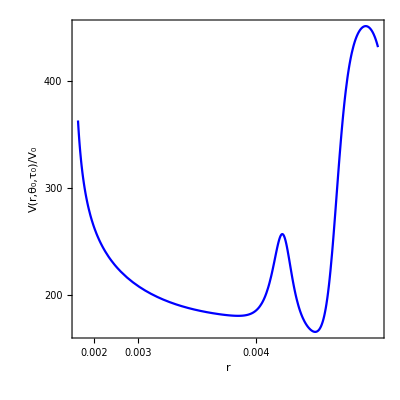

```mathematica
Plot[Chop[Vr,5],{r,0.001,0.0045},PlotTheme->"Scientific",PlotStyle->Blue, FrameLabel -> {
   "r",
   "V(r,θ_0,τ_0)/V_0"
 }, LabelStyle -> {FontFamily -> "Times", FontSize -> 14, FontColor -> Black},
  LabelStyle -> {FontFamily -> "Times", FontSize -> 14, FontColor -> Black},AspectRatio->1,ScalingFunctions->{{Exp[1000 #]&,1/1000*Log[#]&},None},
  FrameTicks->{{{200,400,300
  },None},{{0.002,{0.0025,""},0.003,{0.0035,""},0.004,{0.0045,""}},None}}
 ]
```

```mathematica
r0
```

-420.87220520328238181799102381872449550150721873189-2.8949543604850336891129220827461502347705335258047×10^-55 ⅈ

```mathematica
p0
```

0.24974621594968777809590773063431465018387720021878

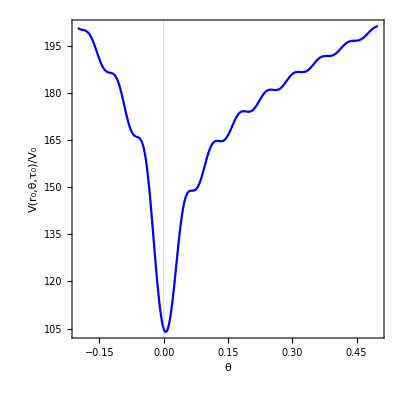

```mathematica
Plot[Chop[Vp,5],{p,-0.2,0.5}, PlotTheme->"Scientific", PlotStyle->Blue, FrameLabel -> {
   "θ",
   "V(r_0,θ,τ_0)/V_0"
 }, LabelStyle -> {FontFamily -> "Times", FontSize -> 14, FontColor -> Black}, Ticks -> {{#, ScientificForm@#} & /@ 
    Range[0., 100., 20.], {#, ScientificForm@#} & /@ 
    Range[0., 0.100^2, 0.1000]},AspectRatio->1]
```

```mathematica
t10
```

-1.2214265545494748157014894784071121961939014630987

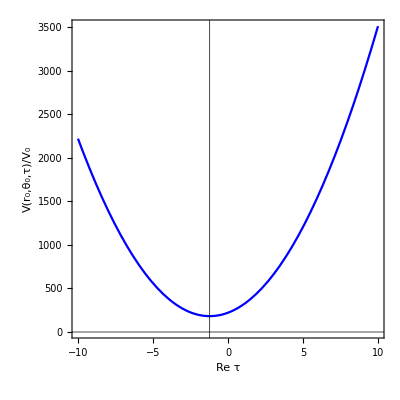

```mathematica
Plot[Vt1,{tau1,-10,10}, PlotTheme->"Scientific", PlotStyle->Blue ,PlotStyle->Black,GridLines->{{t10}},GridLinesStyle->Black, LabelStyle -> {FontFamily -> "Times", FontSize -> 14, FontColor -> Black}, Ticks -> {{#, ScientificForm@#} & /@ 
    Range[0., 100., 20.], {#, ScientificForm@#} & /@ 
    Range[0., 100^2, 1000.]},  PlotStyle->Blue, FrameLabel -> {
   "Re τ",
   "V(r_0,θ_0,τ)/V_0"
 },AspectRatio->1]
```

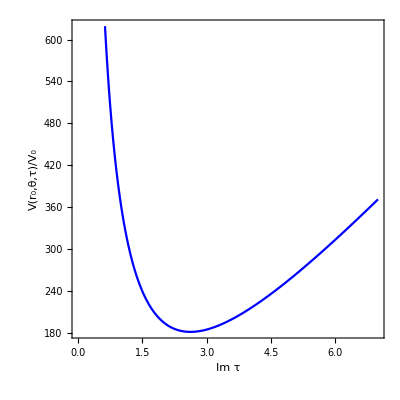

```mathematica
Plot[Vt2,{tau2,0,7},  PlotTheme->"Scientific", PlotStyle->Blue ,PlotStyle->Black,GridLines->{{t10}},GridLinesStyle->Black, LabelStyle -> {FontFamily -> "Times", FontSize -> 14, FontColor -> Black}, Ticks -> {{#, ScientificForm@#} & /@ 
    Range[0., 100., 20.], {#, ScientificForm@#} & /@ 
    Range[0., 100^2, 1000.]},  PlotStyle->Blue, FrameLabel -> {
   "Im τ",
   "V(r_0,θ,τ)/V_0"
 },AspectRatio->1]
```

```mathematica
Vgraf=ReplaceAll[ReplaceAll[Vcomp,{Log[zc]->-I p+Log[r],Log[z]->I p+Log[r]}],{z->r (Cos[p]+I Sin[p]),zc->r (Cos[ p]-I Sin[p]),t->tau1+I tau2,tc->tau1-I tau2}];
```

```mathematica
Vrpt1 = Vgraf/.tau2->t20;
```

```mathematica
Vt1t2 = Vgraf/.r->r0 /. p->p0;
Vrp = Vgraf/.tau1->t10/.tau2->t20;
Vt1r =Vgraf/.p->p0/.tau2->t20;
Vt2r= Vgraf/.tau1->t10/.p->p0;
Vpt1 = Vgraf/.r->r0/.tau2->t20;
Vpt2 = Vgraf/.tau1->t10/.r->r0;
```

```mathematica
t10
t20
```

-1.2214265545494748157014894784071121961939014630987

2.6236117391903211701953159959094561600202203343949

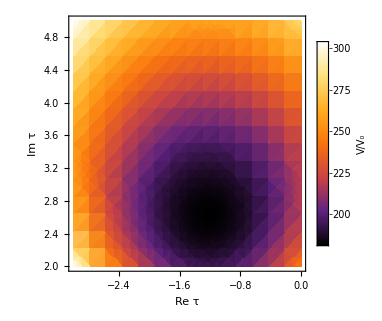

```mathematica
V1 = DensityPlot[Vt1t2, {tau1,-3,0},{tau2,2,5},ColorFunction->"SunsetColors",PlotLegends->BarLegend[Automatic,LegendLabel->"V/V_0"], FrameLabel->{"Re τ"," Im τ"}, LabelStyle -> {FontFamily -> "Times", FontSize -> 14, FontColor -> Black}]
```

```mathematica
Export["Untitled5.png",V1]
```

Untitled5.png

```mathematica
r0
p0
```

0.0038982627244953723071093837692684805980015732472507

0.24974621594968777809590773063431465018387720021878

```mathematica
0.003896,0.00390
```

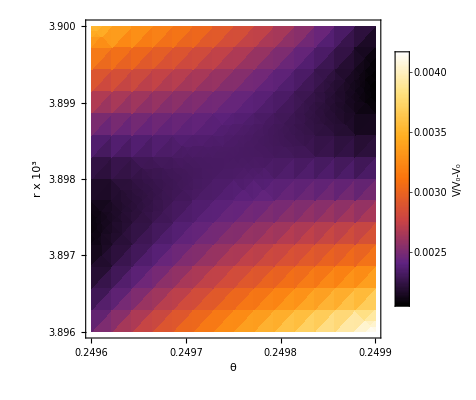

```mathematica
V2 = DensityPlot[Vrp , {p, 0.24960,0.2499},{r, 0.003896,0.00390},ColorFunction->"SunsetColors",PlotLegends->BarLegend[Automatic(*,LabelingFunction->((#-181.000)&)*),"Ticks"->{181.0025,181.0030,181.0035,181.0040},"TickLabels"->{"0.0025","0.0030","0.0035","0.0040"},LegendLabel->"V/V_0-V_0"], PlotLegends->Automatic, FrameLabel->{"θ","r x 10^3"}, LabelStyle -> {FontFamily -> "Times", FontSize -> 14, FontColor -> Black}, FrameTicks->{{{{0.003896,"3.896"},{0.003897,"3.897"},{0.003898,"3.898"},{0.003899,"3.899"},{0.003900,"3.900"}},None},{{0.2496, 0.2497,0.2498,0.2499},None}}]
```

```mathematica
≥
```

```mathematica
Export["Untitled6.png",V2]
```

Untitled6.png

```mathematica
t10
r0
```

-1.2214265545494748157014894784071121961939014630987

0.0038982627244953723071093837692684805980015732472507

```mathematica
(*{r, 0.0036,0.0040},{tau1,-2,-0.5} BUENA aprox*)
```

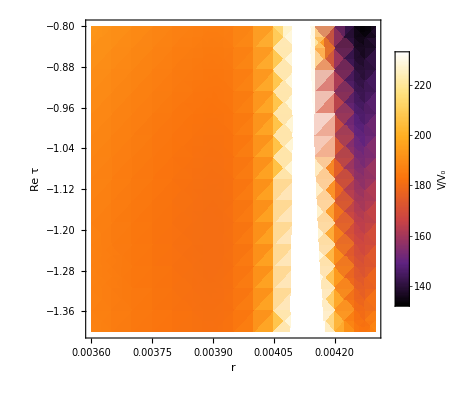

```mathematica
V7=DensityPlot[Vt1r,{r, 0.0036,0.0043},{tau1,-1.4,-0.8},ColorFunction->"SunsetColors",PlotLegends->BarLegend[Automatic,LegendLabel->"V/V_0"], FrameLabel->{"r"," Re τ"}, LabelStyle -> {FontFamily -> "Times", FontSize -> 14, FontColor -> Black}]
```

```mathematica
Export["Untitled7.png",V7]
```

Untitled7.png

```mathematica
t20
r0
```

2.6236117391903211701953159959094561600202203343949

0.0038982627244953723071093837692684805980015732472507

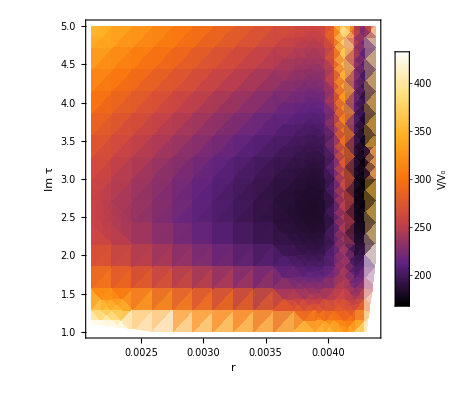

```mathematica
V8=DensityPlot[Vt2r, {r, 0.0021,0.00438},{tau2,1,5},ColorFunction->"SunsetColors",PlotLegends->BarLegend[Automatic,LegendLabel->"V/V_0"],FrameLabel->{"r"," Im τ"}, LabelStyle -> {FontFamily -> "Times", FontSize -> 14, FontColor -> Black}]
```

```mathematica
Export["Untitled8.png",V8]
```

Untitled8.png

```mathematica
t10
p0
```

-1.2214265545494748157014894784071121961939014630987

0.24974621594968777809590773063431465018387720021878

```mathematica
t10+0.5 t10
t20-0.5 t10
```

-1.83214

3.23433

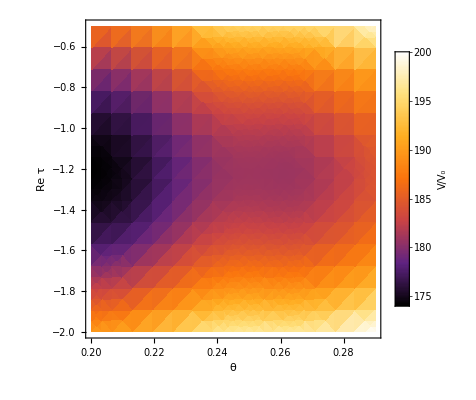

```mathematica
V9 =DensityPlot[Vpt1 ,{p, 0.2,0.290}, {tau1,-2,-0.5},ColorFunction->"SunsetColors",PlotLegends->BarLegend[Automatic,LegendLabel->"V/V_0"], FrameLabel->{"θ","Re τ"}, LabelStyle -> {FontFamily -> "Times", FontSize -> 14, FontColor -> Black}]
```

```mathematica
Export["Untitled9.png",V9]
```

Untitled9.png

```mathematica
t20
```

2.6236117391903211701953159959094561600202203343949

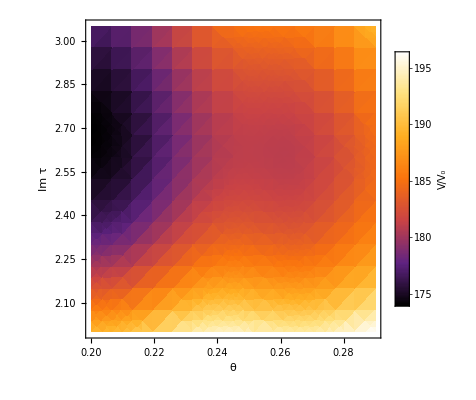

```mathematica
V10 =DensityPlot[Vpt2, {p, 0.2,0.290},{tau2,2,3.05},ColorFunction->"SunsetColors",PlotLegends->BarLegend[Automatic,LegendLabel->"V/V_0"], FrameLabel->{"θ","Im τ"}, LabelStyle -> {FontFamily -> "Times", FontSize -> 14, FontColor -> Black}]
```

```mathematica
Export["Untitled10.png",V10]
```

Untitled10.png

```mathematica
leadingSeries2[expr_, z_,zc_] := Normal[Series[expr /.{z->(z+O[z]^2),zc->(zc+O[zc]^2)},{z,0,1}]]
PiC={wM0,wM1,wM2,wM3};
x0 = wM0;
x1 =1/(2 Pi I)(wM0 Log[z] + wM1);
te = x1/x0//Simplify;
T = Series[t,{z,0,2}];
tee= T/.z->1/(5^5 ψ) /. Log[1/(3125 ψ)]->Log[1]-Log[5^5 ψ] //Simplify;
tee = - 5/(2 Pi I) Log[5 ψ];
Print["t = ", t]
Periods = (2 Pi I / 5)^3 {5/6 t^3 + 25/12 t, -5/2 t^2 -1/2 t, 1, t};
Print["Periods =", MatrixForm[Periods]]
PeriodsC = Conjugate[Periods]/. Conjugate[ψ]->ψc /. Conjugate[Log[5 ψ]]-> Log[ 5ψc];
Σ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}};

etomK =  -16/375 π^3 Log[5 ψ] (-10 Log[5 ψ]^2)/. Log[5 ψ]-> -(2 Pi I)/5 f ;
Print["e^-K=", etomK]
Ka = -Log[etomK];
Print["K =", Ka]
g =  D[Ka,f,f];
Print["2∂_(ψ, ψ) K = ", g/2]
d = Integrate[Sqrt[g/2],f];
Print["d = ",d]
```

General::ivar: 1/(3125 ψ) is not a valid variable.

SeriesData::sdatv: First argument 1/(3125 ψ) is not a valid variable.

t = Log[z]+34 z+1435 z^2+O[z]^3

Periods =(-8/125 ⅈ π^3 ((25 Log[z])/12+(5 Log[z]^3)/6)-8/125 ⅈ π^3 (425/6+85 Log[z]^2) z-8/125 ⅈ π^3 (35875/12+5/6 (3468/Log[z]^2+4305/Log[z]) Log[z]^3) z^2+O[z]^3
-8/125 ⅈ π^3 (-Log[z]/2-(5 Log[z]^2)/2)-8/125 ⅈ π^3 (-17-170 Log[z]) z-8/125 ⅈ π^3 (-1435/2-5/2 (1156+2870 Log[z])) z^2+O[z]^3
-(8 ⅈ π^3)/125
-8/125 ⅈ π^3 Log[z]-272/125 ⅈ π^3 z-2296/25 ⅈ π^3 z^2+O[z]^3)

e^-K=(256 ⅈ f^3 π^6)/9375

K =-Log[(256 ⅈ f^3 π^6)/9375]

2∂_(ψ, ψ) K = 3/(2 f^2)

d = √(3/2) √(1/f^2) f Log[f]